```mathematica
PointsPA = {{0.10, 0.20},{0.10,0.30},{0.1,0.40},{0.50,0.20},{0.50,0.30},{0.50,0.40},{0.90,0.20},{0.90,0.30},{0.90,0.40}};
```

```mathematica
ValueP120 = {};
For[i=1,i≤ Length[PointsPA],i++,
ValueP120 = Insert[ValueP120,BEMP[PointsPA[[i,1]],PointsPA[[i,2]]],-1]
]
ValueP120
```

{0.253738,0.374381,0.488345,0.326665,0.469776,0.595548,0.771894,0.895153,0.976404}

```mathematica
ValueP60 ={};
For[i=1,i≤ Length[PointsPA],i++,
ValueP60 = Insert[ValueP60,BEMP[PointsPA[[i,1]],PointsPA[[i,2]]],-1]
]
ValueP60
```

{0.253818,0.374508,0.488517,0.326754,0.469958,0.595803,0.773119,0.896111,0.977072}

```mathematica
PointsPAPolar  = {};
For[i = 1,i≤ Length[PointsPA],i++,
PointsPAPolar = Insert[PointsPAPolar,CoordinateTransform["Cartesian" -> "Polar",PointsPA[[i]] ],-1]
]
PointsPAPolar
```

{{0.223607,1.10715},{0.316228,1.24905},{0.412311,1.32582},{0.538516,0.380506},{0.583095,0.54042},{0.640312,0.674741},{0.921954,0.218669},{0.948683,0.321751},{0.984886,0.418224}}

```mathematica
ValueExact = {};
For[i=1,i≤ Length[PointsPAPolar],i++,
ValueExact= Insert[ValueExact,AnalyticSolution[PointsPAPolar[[i,1]],PointsPAPolar[[i,2]]],-1]
]
ValueExact
```

{0.253707,0.374334,0.488284,0.326623,0.469708,0.595458,0.771599,0.894863,0.976138}

```mathematica
PointsPA2 = {{0.1,0.95},{0.1,0.96},{0.1,0.97},{0.1,0.98},{0.1,0.99}}
```

{{0.1,0.95},{0.1,0.96},{0.1,0.97},{0.1,0.98},{0.1,0.99}}

```mathematica
PointsPAPolar2  = {};
For[i = 1,i≤ Length[PointsPA2],i++,
PointsPAPolar2 = Insert[PointsPAPolar2,CoordinateTransform["Cartesian" -> "Polar",PointsPA2[[i]] ],-1]
]
PointsPAPolar2
```

{{0.955249,1.46592},{0.965194,1.467},{0.975141,1.46807},{0.985089,1.46911},{0.995038,1.47013}}

```mathematica
ValueExact2 = {};
For[i=1,i≤ Length[PointsPAPolar2],i++,
ValueExact2= Insert[ValueExact2,AnalyticSolution[PointsPAPolar2[[i,1]],PointsPAPolar2[[i,2]]],-1]
]
ValueExact2
```

{0.970703,0.97733,0.983891,0.990386,0.996817}

```mathematica
ValueP1202={};
For[i=1,i≤ Length[PointsPA2],i++,
ValueP1202 = Insert[ValueP1202,BEMP[PointsPA2[[i,1]],PointsPA2[[i,2]]],-1]
]
ValueP1202
```

{0.970805,0.977433,0.983994,0.990491,0.996929}

```mathematica
(ValueP1202 - ValueExact2 )
```

{0.000102288,0.000102576,0.000103059,0.00010473,0.000112379}

```mathematica
PointsPA3 = {};
For [i = 1,i ≤ 180,i++,
PointsPA3 = Insert[PointsPA3,N[CoordinateTransform["Polar"-> "Cartesian",{1, i/180 π}],10],-1]
]
```

```mathematica
ValueP1203={};
For[i=1,i≤ Length[PointsPA3],i++,
ValueP1203 = Insert[ValueP1203,BEMP[PointsPA3[[i,1]],PointsPA3[[i,2]]],-1]
]
```

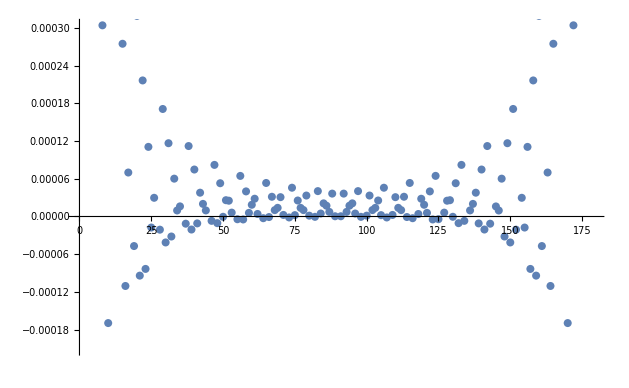

```mathematica
Show[ListPlot[ValueP1203],ListPlot[ConstantArray[1,180]]]
```